Evolution of sex roles: Mathematical analysis

Xiaoyan Long and Franz J. Weissing


 Figure 1a: 
 (TM -  male care, TF - female care, d - care demand of offspring, u - mortality rate, 
 sgMale - selection gradient for male care; sgFemale - selection gradient for female care)

{d→20,u→0.001}

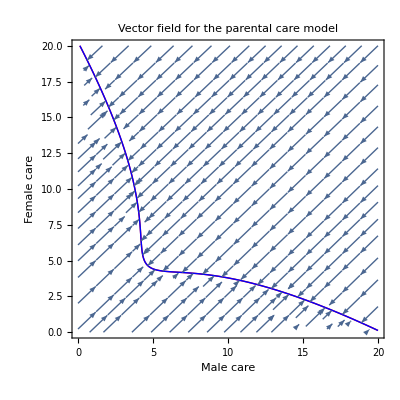

```mathematica
ClearAll["Global'*"]

sgMale[TM_,TF_]:=(2 * d^2 *ⅇ^(-TM u))/(((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2 + d^2)*(((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))) +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *(-u)*ⅇ^(-TM u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *  ⅇ^(-TM u))

sgFemale[TM_,TF_]:=(2 *d^2 *ⅇ^(-TF u))/(((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2 + d^2)*(((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u )))  +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *(-u)*ⅇ^(-TF u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *  ⅇ^(-TF u))

pars={d->20,u->0.001}

plot1=ContourPlot[sgMale[TM,TF]/.pars,{TM,0,20},{TF,0,20},Contours->{0},ContourShading->None,ContourStyle->Red,MaxRecursion->10];
plot2=ContourPlot[sgFemale[TM,TF]/.pars,{TM,0,20},{TF,0,20},Contours->{0},ContourShading->None,ContourStyle->Blue,MaxRecursion->10];
plot3=StreamPlot[{sgMale[TM,TF],sgFemale[TM,TF]}/.pars,{TM,0,20},{TF,0,20}];
Show[{plot1,plot2,plot3}, PlotLabel-> "Vector field for the parental care model", FrameLabel-> {"Male care",  "Female care"}]
```

Supplementary Figure S5a: 
 (TM -  male care, TF - female care, a - the parameter of offspring survival function in Fromhage and Jennions (2016), u - mortality rate, 
 SGmale - selection gradient for male care; SGfemale - selection gradient for female care.)

{a→0.1,u→0.01}

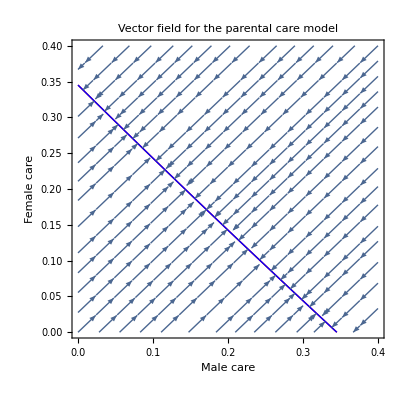

```mathematica
ClearAll["Global'*"]

SGmale[TM_,TF_]:=(a *ⅇ^(-TM u))/((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2)  +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *(-u)*ⅇ^(-TM u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *  ⅇ^(-TM u))
SGfemale[TM_,TF_]:=(a *ⅇ^(-TF u))/((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2) +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *(-u)*ⅇ^(-TF u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *  ⅇ^(-TF u))

pars={a->0.1,u->0.01}

plot1=ContourPlot[SGmale[TM,TF]/.pars,{TM,0,0.4},{TF,0,0.4},Contours->{0},ContourShading->None,ContourStyle->Red,MaxRecursion->10];
plot2=ContourPlot[SGfemale[TM,TF]/.pars,{TM,0,0.4},{TF,0,0.4},Contours->{0},ContourShading->None,ContourStyle->Blue,MaxRecursion->10];
plot3=StreamPlot[{SGmale[TM,TF],SGfemale[TM,TF]}/.pars,{TM,0,0.4},{TF,0,0.4}];
Show[{plot1,plot2,plot3}, PlotLabel-> "Vector field for the parental care model", FrameLabel-> {"Male care",  "Female care"}]
```

Supplementary Figure S5b: 
 (TM -  male care, TF - female care, a - the parameter of offspring survival function in Fromhage and Jennions (2016), u - mortality rate, 
 SGmale - selection gradient for male care; SGfemale - selection gradient for female care.)

{a→20,u→0.001}

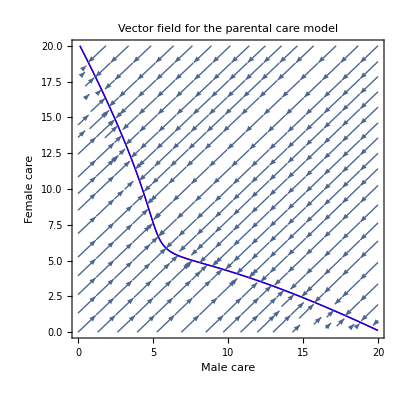

```mathematica
ClearAll["Global'*"]

SGmale[TM_,TF_]:=(a *ⅇ^(-TM u))/((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2)  +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *(-u)*ⅇ^(-TM u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(-1/2)+u) *  ⅇ^(-TM u))
SGfemale[TM_,TF_]:=(a *ⅇ^(-TF u))/((((1-ⅇ^(-TM u))/u )+((1-ⅇ^(-TF u))/u ))^2) +(((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *(-u)*ⅇ^(-TF u))/(1- ((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2))/((1+ (ⅇ^(-TM u)-ⅇ^(-TF u))/(2*u*u)*((ⅇ^(-TM u)-ⅇ^(-TF u))+((ⅇ^(-TM u)-ⅇ^(-TF u))*(ⅇ^(-TM u)-ⅇ^(-TF u))+4*u*u)^(1/2)))^(1/2)+u) *  ⅇ^(-TF u))

pars={a->20,u->0.001}

plot1=ContourPlot[SGmale[TM,TF]/.pars,{TM,0,20},{TF,0,20},Contours->{0},ContourShading->None,ContourStyle->Red,MaxRecursion->10];
plot2=ContourPlot[SGfemale[TM,TF]/.pars,{TM,0,20},{TF,0,20},Contours->{0},ContourShading->None,ContourStyle->Blue,MaxRecursion->10];
plot3=StreamPlot[{SGmale[TM,TF],SGfemale[TM,TF]}/.pars,{TM,0,20},{TF,0,20}];
Show[{plot1,plot2,plot3}, PlotLabel-> "Vector field for the parental care model", FrameLabel-> {"Male care",  "Female care"}]
```

Supplementary Figure S2: 
 (TM -  male care, TF - female care, a - the parameter of offspring survival function in Fromhage and Jennions (2016), u - mortality rate, 
 SGmale - selection gradient for male care; SGfemale - selection gradient for female care.)

```mathematica
ClearAll["Global'*"]
fitRes[T_] := ((T+T)^2/((T+T)^2+ d^2)) * (1/(1+u -ⅇ^(-T * u)))
fitMut[T_, Tmut_] := ((T+Tmut )^2/((T+Tmut )^2+d^2)) * (1/(1+u -ⅇ^(-Tmut* u)))
grad [T_]:= D[fitMut[T, Tmut]  , Tmut]/.{Tmut->T} // FullSimplify
eq = grad [T]==0
FindRoot[eq /.{u->  0.001,d-> 20},{T,0.0001,20}]
deltaW = fitMut[T, Tmut]-fitRes[T]
p1 = ContourPlot[deltaW /. {u->  0.001, r -> 0,D-> 20},{T,0.0,20.0},{Tmut,0.0,20.0},Contours->{0},PlotPoints->100,PlotRange->All,ContourShading->{Blue,Red},
LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
p2 = ContourPlot [T == 4.665565694341089, {T,0.0,20.0},{Tmut,0.0,20.0},ContourStyle-> {White,Dashed},LabelStyle->Directive[FontFamily->"Arial",FontSize->20]]
Show[p1,p2]
```

SetDelayed::write: Tag Times in (4 ⅇ^(T u) T (-4 T^3 u+D^2 (-1-T u+ⅇ^(T u) (1+u))))/((D^2+4 T^2)^2 (-1+ⅇ^(T u) (1+u))^2)[T_] is Protected.

$Failed

(4 ⅇ^(T u) T (-4 T^3 u+D^2 (-1-T u+ⅇ^(T u) (1+u))))/((D^2+4 T^2)^2 (-1+ⅇ^(T u) (1+u))^2)==0

FindRoot::nlnum: The function value {(399.92 (-4.×10^-15+0.001 D^2))/((4.×10^-8+D^2)^2)} is not a list of numbers with dimensions {1} at {T} = {0.0001}.

FindRoot[eq/.{u→0.001,d→20},{T,0.0001,20}]

-(4 T^2)/((d^2+4 T^2) (1-ⅇ^(-T u)+u))+(T+Tmut)^2/((d^2+(T+Tmut)^2) (1-ⅇ^(-Tmut u)+u))